(180 (-20 °+Tan[20 °]))/π

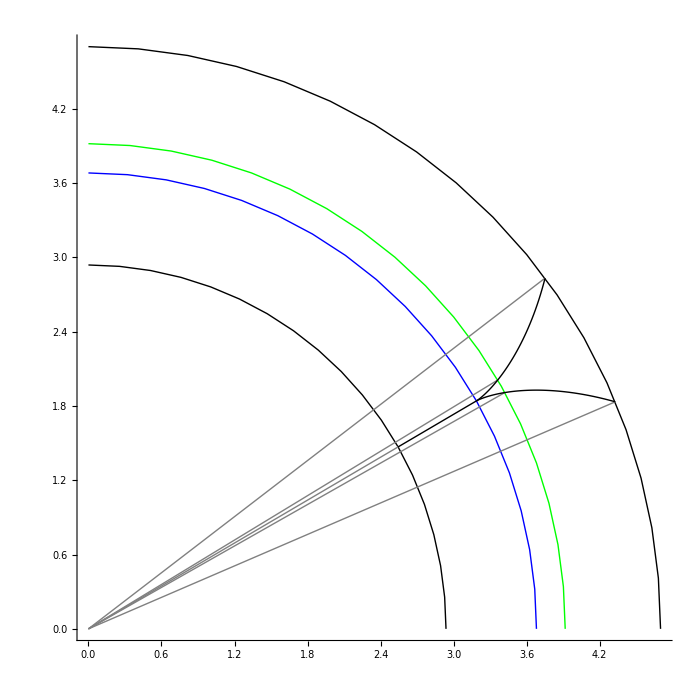

```mathematica
α=20°;
Subscript[d, a]=9.4;31.3;
z=10;38;
m=Subscript[d, a]/(z+2);
d=Subscript[d, a]-2 m;
Subscript[d, b]=d Cos[α];
Subscript[d, f]=m(z-2.5);
ϕ=30°;
ω=√(Subscript[d, a]^2/Subscript[d, b]^2-1)-ArcCos[Subscript[d, b]/Subscript[d, a]];ω*180/π;
Subscript[ω, 0]=Tan[α]-α; Subscript[ω, 0]*180/π
Show[
Graphics[{Green, Thin,Circle[{0,0},d/2 ,{0°,90°}], Blue, Thin, Circle[{0,0},Subscript[d, b]/2,{0°,90°}], Black, Thick, Circle[{0,0},Subscript[d, a]/2,{0°,90°}], Black, Thick, Circle[{0,0},Subscript[d, f]/2,{0°,90°}]}],
ParametricPlot[{r Cos[ϕ],r Sin[ϕ]},{r,Subscript[d, f]/2,Subscript[d, b]/2},PlotStyle->{Black, Thick}],
ParametricPlot[{r Cos[ϕ],r Sin[ϕ]},{r,0,Subscript[d, f]/2},PlotStyle->{Gray, Thin}],
ParametricPlot[{{r Cos[ϕ+Subscript[ω, 0]],r Sin[ϕ+Subscript[ω, 0]]},{r Cos[ϕ-Subscript[ω, 0]],r Sin[ϕ-Subscript[ω, 0]]}},{r,0,d/2},PlotStyle->{{Gray, Thin}, {Gray, Thin}}],
ParametricPlot[{{r Cos[ω+ϕ],r Sin[ω+ϕ]},{r Cos[ϕ-ω],r Sin[ϕ-ω]}}, {r, 0,Subscript[d, a]/2}, PlotStyle->{{Gray, Thin}, {Gray, Thin}}],
ParametricPlot[{Subscript[d, b]/2 Cos[ψ+ϕ]+Subscript[d, b]/2 ψ Sin[ψ+ϕ],Subscript[d, b]/2 Sin[ψ+ϕ]-Subscript[d, b]/2 ψ Cos[ψ+ϕ]},{ψ,0,√(Subscript[d, a]^2/Subscript[d, b]^2-1)},PlotStyle->{Black, Thick}],
ParametricPlot[{Subscript[d, b]/2 Cos[ϕ-ψ]-Subscript[d, b]/2 ψ Sin[ϕ-ψ],Subscript[d, b]/2 Sin[ϕ-ψ]+Subscript[d, b]/2 ψ Cos[ϕ-ψ]},{ψ,0,√(Subscript[d, a]^2/Subscript[d, b]^2-1)},PlotStyle->{Black, Thick}],
Axes->True,
ImageSize-> 700]
```